# Mathematica Notebook for: “On the smooth unfolding of bifurcations in quantal-response equilibria” Games and Economic Behavior (2023), Adam Harris, Scott McCallum & Michael S. Harré. - Special issue: 25+ years of Quantal Response Equilibrium

### This notebook provides the Mathematica code for generating each of the diagrams in the Games and Economic Behavior (GEB 2023) paper, together with contextualising comments for each code fragment and its diagram. We include here a superset of the diagrams from the GEB (2023) paper, in order to illustrate better the capability of our software. Figure 5 of GEB (2023) is a good place to introduce the computational work that numerically illustrates the results of the paper, starting with Equation 3 near Figure 5: ω_1(x,y) = x + (1-2y)/(1-2x)Log[y/(1-y)]x(1-x) ω_2(x,y) = ω_1(y,x) = y + (1-2x)/(1-2y)Log[x/(1-x)]y(1-y) if we impose the condition ω_1 = ω_2, it follows that x = y, so we can define the simpler form: h(x) := ω(x,x) = x + Log[x/(1-x)]x(1-x) So while ω_i is generically a function of both x and y here we assume that ω_1= ω_2 and as a consequence x = y by Proposition 4.1. This leads us to plotting the diagonal along the x = y line of what is a 2-surface in ℝ^3 (illustrated later as two “sheets”) and consequently we are plotting all of the “triple branch points” of the QRE (excluding the ω_(1/2)=0.5 special case discussed further down this notebook). These assumptions are covered, including the analysis leading to the consequence that the triple branch points lie on the x = y diagonal, at Proposition 4.1 and the related discussion in GEB (2023). Note that for all -0.1 < ω < 0 and 1.0 < ω < 1.1 there are two triple branch points, these are the blue dots shown on the QRE surface towards the end of this notebook and also shown in Figure 7 of GEB (2023). The function ω(x,x) is plotted next and corresponds to Figure 5 in GEB (2023):

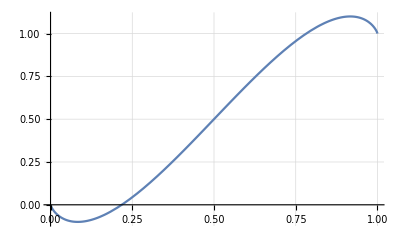

```mathematica
Plot[ω = x+ Log[x/(1-x)]x(1-x),{x,0,1},GridLines->Automatic, PlotRange->All]
```

### This is a special case of the more general function ρ(x,y) that defines all critical points (triple branch points and fold points) given by: ρ(x,y) = Log[(1-x)/x]Log[(1-y)/y] - (x-ω)/(x(1-x))(y-ω)/(y(1-y)) = 0 Substituting x = y into this gives both the triple branch points shown above and the points at which folds occur along the x = y diagonal: 0 = (Log[(1-x)/x])^2 - ((x-ω)/(x(1-x)))^2 We can solve this explicitly for ω and we find two solutions that are the two distinct critical points for every ω given the x = y assumption, one is a triple branch point and one is a fold point when 0 < ω < 1, or both are triple branch points in the case where -0.1 < ω < 0 or 1.0 < ω < 1.1:

{{ω→x+(-1+x) x Log[-1+1/x]},{ω→x-(-1+x) x Log[-1+1/x]}}

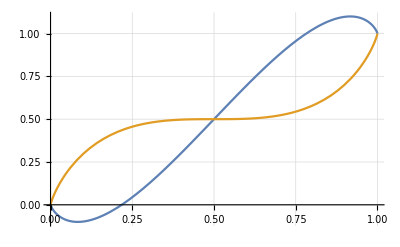

```mathematica
SolnOne=FullSimplify[Solve[Log[(1-x)/x]Log[(1-x)/x]-(x-ω)/(x(1-x))(x-ω)/(x(1-x))==0,ω]]
Plot[{ω/.SolnOne⟦1⟧,ω/.SolnOne⟦2⟧},{x,0,1},GridLines->Automatic]
```

### It is also possible to generate a solution for the general case in which ρ(x,y) = 0 ∀ x,y ∈ [0,1]. The full solution is composed of two sheets that touch at only three isolated points (x,y) = {(0,0),(1/2,1/2), (1,1)}, we label the two resulting “sheets” ω^+ and ω^- for the top and bottom surfaces respectively:

```mathematica
FullAns = FullSimplify[Expand[Solve[Log[(1-x)/x]Log[(1-y)/y]-(x-ω)/(x(1-x))(y-ω)/(y(1-y))==0,ω]]]
```

{{ω→1/2 (x+y+(-1+x) x (-1+y) y √(((x-y)^2+4 (-1+x) x (-1+y) y Log[-1+1/x] Log[-1+1/y])/((-1+x)^2 x^2 (-1+y)^2 y^2)))},{ω→1/2 (x+y+x y (-1+x+y-x y) √(((x-y)^2+4 (-1+x) x (-1+y) y Log[-1+1/x] Log[-1+1/y])/((-1+x)^2 x^2 (-1+y)^2 y^2)))}}

### This simplifies to the expression for ω_inear Figure 3 in GEB (2023). We can now plot the complete set of all possible triple branch points and fold points, i.e. all critical points of the QRE potential function related to all possible 2x2 games parameterised by ω_i values. This is two sheets of solutions embedded in ℝ^3:

```mathematica
GraphicsGrid[{{
Plot3D[{ω/.FullAns⟦1⟧,ω/.FullAns⟦2⟧},{x,0,1},{y,0,1},BoxRatios->{1,1,1},AxesLabel->{x,y,Subscript[ω, i]},LabelStyle->Directive[16]],Plot3D[{ω/.FullAns⟦1⟧},{x,0,1},{y,0,1},BoxRatios->{1,1,1},AxesLabel->{x,y,Subscript[ω, i]},LabelStyle->Directive[16]],
Plot3D[{ω/.FullAns⟦2⟧},{x,0,1},{y,0,1},BoxRatios->{1,1,1},AxesLabel->{x,y,Subscript[ω, i]},LabelStyle->Directive[16],PlotStyle->Blue]
}}]
```

-Graphics-

### The contour plot for these equations are derivable via an implicit numerical scheme. First we want to know which is the top sheet and which is the bottom sheet, so we plot the two contours, one contour from each sheet, where the contours correspond to different signs in their functions. In this example we have set the level set to be ω = 0.4 and the result is a contour generated by a horizontal plane slicing through the middle and the right hand plots immediately above, parallel to the (x,y) coordinate plane:

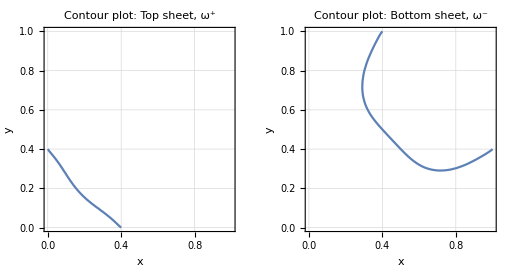

```mathematica
GraphicsGrid[{{ContourPlot[
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==0.4,
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot: Top sheet, ω^+",20],FrameLabel->{x,y} ,LabelStyle->Directive[16],ImageSize->Full],
ContourPlot[
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==0.4,
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot: Bottom sheet, ω^-",20],FrameLabel->{x,y} ,LabelStyle->Directive[16],ImageSize->Full]}}]
```

### If we compare these two plots to the sheets plotted above, we can see by inspection that the left contour belongs to ω^+ and the right contour belongs to ω^-. We can then plot the complete family of contours for many different values of ω^(+/-) for these sheets, resulting in two contour plots, one for ω^+ and one for ω^-. Each label on the contours below match between the two plots, for example a ω^+ = 0.25 on the left plot corresponds to the matching ω^- = 0.25 on the right, this is Figure 3 in GEB (2023):

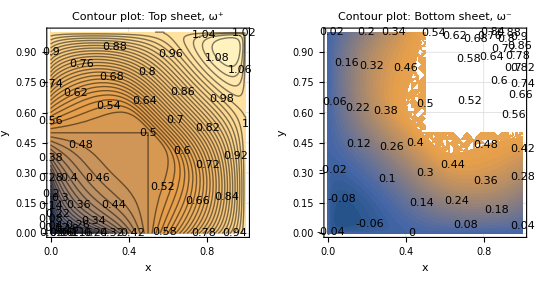

```mathematica
A = ContourPlot[
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2)),
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot: Top sheet, ω^+",20],FrameLabel->{x,y} ,LabelStyle->Directive[16],Contours->{Automatic,60} , ContourLabels->True];
B = ContourPlot[
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2)),
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot: Bottom sheet, ω^-",20],FrameLabel->{x,y} ,LabelStyle->Directive[16],Contours->{Automatic,60} , ContourLabels->True];
GraphicsGrid[{{A,B}}]
```

### We can’t directly combine the whole family of contours on one plot, but for any given ω value we can plot the two ω^(+/-) critical sets that correspond to the two sheets on a single plot:

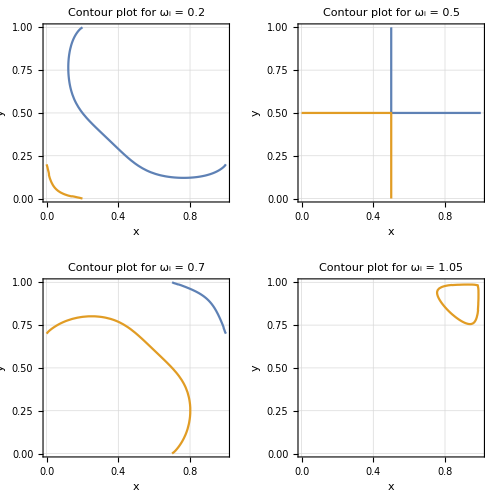

```mathematica
ω = 0.2;
A = ContourPlot[{
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω_i = "<>ToString@ω,Bold,16,Black],FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
ω = 0.5;
B = ContourPlot[{
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω_i = "<>ToString@ω,Bold,16,Black],FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
ω = 0.7;
F= ContourPlot[{
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω_i = "<>ToString@ω,Bold,16,Black],FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
ω = 1.05;
H = ContourPlot[{
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω_i = "<>ToString@ω,Bold,16,Black],FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
GraphicsGrid[{{A,B},{F,H}}]
```

### We also have the two exceptional cases of ω > 1 and ω < 0, which play a central role in the GEB (2023) paper as they correspond to the pleated loop, see Theorem 5.2 in GEB (2023). Note that these critical sets form closed loops in the contour plane above (bottom right figure), once these loops are “lifted” onto the QRE surface (see below) they correspond to the pleated loop plotted in Figure 7 of GEB (2023). Two examples are shown below:

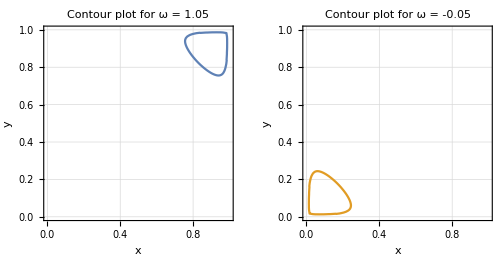

```mathematica
ω = 1.05;
A = ContourPlot[{
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω = "<>ToString@ω,Bold,16,Black],FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
ω = -0.05;
B = ContourPlot[
{1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω ,
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω },
{x,0,1}, {y,0,1}, PlotRange-> {{0,1},{0,1}},GridLines->Automatic, PlotLabel->Style["Contour plot for ω = "<>ToString@ω,Bold,16,Black] ,FrameLabel->{x,y} ,LabelStyle->Directive[16], ContourLabels->True];
GraphicsGrid[{{A,B}}]
```

# Constructing Slices Through a QRE Surface

### Initially we define a function for y as a function of x, ω_1, ω_2, κ_1, and κ_2 with δ defining a perturbation of the slice through the QRE surface such that it doesn’t fall exactly on the 45^o line through κ_1= κ_2:

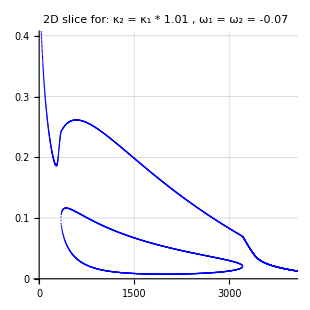

```mathematica
func[κ2_,δ_,ω1_, ω2_] := Log[x/(1-x)]/(-ω1+1/(1+ⅇ^(-(-ω2 + x)κ2)))-κ2 /δ; 
δ = 1.01;
ω2 = -0.07;
ω1 = ω2;
endpt = 100;
stpsz = 0.025;
solns = Flatten[Table[NSolve[func[-κ,δ,ω1,ω2]==0,x,Reals],{κ,0,endpt,stpsz}]];

ListPlot[solns⟦All,2⟧,GridLines->Automatic,PlotRange->{{0.1,endpt/stpsz}, {0,0.4}}, PlotStyle->{Blue,PointSize[0.003]}, PlotLabel->Style["2D slice for: κ_2 = κ_1 * "<>ToString@δ", ω_1 = ω_2 = "<>ToString@ω2,Bold,25,Black],Background->White,PlotLabel->None,LabelStyle->{16,GrayLevel[0]},LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},Ticks->{None,All},AspectRatio->1]
```

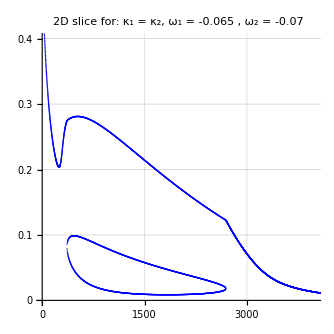

```mathematica
func[κ2_,δ_,ω1_, ω2_] := Log[x/(1-x)]/(-ω1+1/(1+ⅇ^(-(-ω2 + x)κ2)))-κ2 /δ; 
δ =1;
ω2 = -0.07;
ω1 = -0.065;
endpt = 100;
stpsz = 0.025;
solns = Flatten[Table[NSolve[func[-κ,δ,ω1,ω2]==0,x,Reals],{κ,0,endpt,stpsz}]];

ListPlot[solns⟦All,2⟧,GridLines->Automatic,PlotRange->{{0.1,endpt/stpsz}, {0,0.4}}, PlotStyle->{Blue,PointSize[0.003]}, PlotLabel->Style["2D slice for: κ_1 = κ_2, ω_1 = "<>ToString@ω1 ", ω_2 = "<>ToString@ω2,Bold,25,Black],Background->White,PlotLabel->None,LabelStyle->{16,GrayLevel[0]},LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},Ticks->{None,All},AspectRatio->1]
```

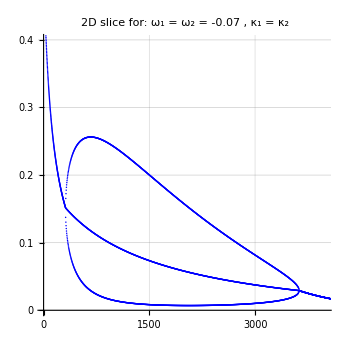

```mathematica
func[κ1_,δ_, ω1_, ω2_] := Log[x/(1-x)]/(-ω1+1/(1+ⅇ^(-(-ω2 + x)κ1)))-κ1/δ; 
δ = 1;
ω1 = -0.07;
ω2 = -0.07;
endpt = 100;
stpsz = 0.025;
solns = Flatten[Table[NSolve[func[-κ,δ,ω1,ω2]==0,x,Reals],{κ,0,endpt,stpsz}]];;

ListPlot[solns⟦All,2⟧,GridLines->Automatic,PlotRange->{{0.1,endpt/stpsz}, {0,0.4}}, PlotStyle->{Blue,PointSize[0.003]}, PlotLabel->Style["2D slice for: ω_1 = ω_2 = " <>ToString@ω2", κ_1 = κ_2 ",Bold,25,Black],Background->White,PlotLabel->None,LabelStyle->{16,GrayLevel[0]},LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},Ticks->{None,All},AspectRatio->1]
```

```mathematica
func[κ2_,δ_,ω1_, ω2_] := Log[x/(1-x)]/(-ω1+1/(1+ⅇ^(-(-ω2 + x)κ2)))-κ2/δ; 
δ = 1.0;
ω2 = 0.75;
ω1 = 0.25;
endpt = 10;
stpsz = 0.0025;
solns = Flatten[Table[NSolve[func[κ,δ,ω1,ω2]==0,x,Reals],{κ,0,endpt,stpsz}]];
```

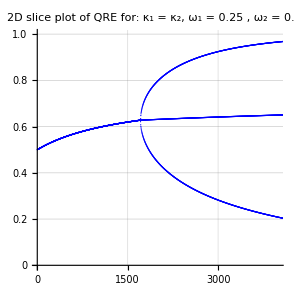

```mathematica
ListPlot[solns⟦All,2⟧,GridLines->Automatic,PlotRange->{{0.1,endpt/stpsz}, {0,1}}, PlotStyle->{Blue,PointSize[0.003]}, PlotLabel->Style["2D slice plot of QRE for: κ_1 = κ_2, ω_1 = "<>ToString@ω1", ω_2 = "<>ToString@ω2,Bold,20,Black],Background->White,PlotLabel->None,LabelStyle->{16,GrayLevel[0]},LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},Ticks->{None,All},AspectRatio->1]
```

```mathematica
func[κ2_,δ_,ω1_, ω2_] := Log[x/(1-x)]/(-ω1+1/(1+ⅇ^(-(-ω2 + x)κ2)))-κ2/δ; 
δ = 1.01;
ω2 = 0.75;
ω1 = 0.25;
endpt = 10;
stpsz = 0.0025;
solns = Flatten[Table[NSolve[func[κ,δ,ω1,ω2]==0,x,Reals],{κ,0,endpt,stpsz}]];
```

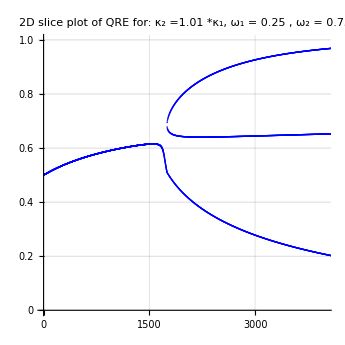

```mathematica
ListPlot[solns⟦All,2⟧,GridLines->Automatic,PlotRange->{{0.1,endpt/stpsz}, {0,1}}, PlotStyle->{Blue,PointSize[0.003]}, PlotLabel->Style["2D slice plot of QRE for: κ_2 =" <>ToString@δ"*κ_1, ω_1 = "<>ToString@ω1", ω_2 = "<>ToString@ω2,Bold,20,Black],Background->White,PlotLabel->None,LabelStyle->{16,GrayLevel[0]},LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},Ticks->{None,All},AspectRatio->1]
```

# Constructing the “Pleated Loop” on the QRE surface

### One of the important results of the GEB (2023) paper is the discovery of the “pleated loop”: For games that have a single Nash Equilibria there exist values of ω_i for which there are 2 uniquely identifiable triple points for finite κ_i. The following code shows how to generate both the QRE surface illustrating this, as well as the critical set that can be overlaid onto the QRE illustrating where the bifurcation sets are. We choose 1 < ω_(1/2) < 1.1 or –0.1 < ω_(1/2) < 0 for which we know there will be a pleated loop, which looks like a closed curve in the level set of critical points in the (x,y) plane. Here we choose ω_1 = ω_2 = ω = –0.07 and the first plot is what we generated above as well:

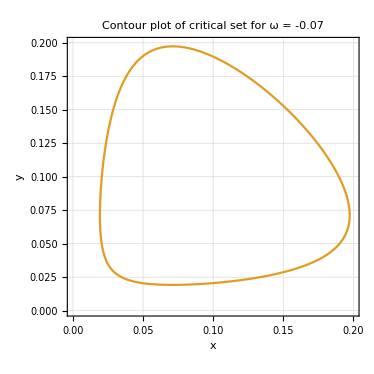

```mathematica
ω = -0.07;
A = ContourPlot[{
1/2((x+y)+((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω,
1/2((x+y)-((x-y)^2+4x(1-x)y(1-y)Log[(1-x)/x]Log[(1-y)/y])^(1/2))==ω},
{x,0,1}, {y,0,1},PlotRange-> {{0,0.2},{0,0.2}},GridLines->Automatic, MaxRecursion->5, PlotLabel->Style["Contour plot of critical set for ω = "<>ToString@ω,Bold,16,Black] ,FrameLabel->{Style["x",16],Style["y",16]} , ContourLabels->True]
```

### Now we take these results from the {x,y} ∈ [0,1]x[0,1] plane and map them to the control plane {κ_1 , κ_2} ∈ ℝ^2

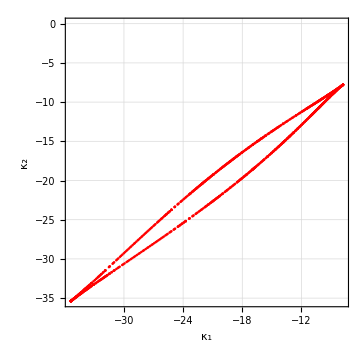

```mathematica
ω1=-0.07;ω2=-0.07;
κ1[{x_,y_}]:=Log[y/(1-y)]/(x-ω1);
κ2[{x_,y_}]:=Log[x/(1-x)]/(y-ω2);
ListPlot[{κ1[#],κ2[#]}&/@A⟦1,1,1⟧,Frame->True,FrameLabel->{Style["κ_1",25],Style["κ_2",25]},LabelStyle-> Directive[{15}],PlotStyle->{Red,PointSize[0.005]},AspectRatio->1,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

### Once we have these data points for the critical points of the pleated loop, (ξ^*)_(1/2) they can be “lifted” from the control plane {κ_1 , κ_2} ∈ ℝ^2 to the space into which each of the two QRE surfaces of each player are embedded, (ξ^*)_i∈ [0,1] x ℝ^2:

```mathematica
bifcurve=ListPointPlot3D[{#⟦1⟧,κ1[#],κ2[#]}&/@A⟦1,1,1⟧,PlotRange->{{0,0.4},{0,-50},{0,-50}},PlotStyle->{Red,PointSize[0.01]}]
```

-Graphics3D-

### We also need to render one of the two QRE surfaces that are embedded in this space, x,y ∈ [0,1] x ℝ^2:

```mathematica
prange = -50;(*plotting bounds*)
CPlot = Plot3D[(Log[x/(1-x)]/(1/(1+ⅇ^(-κ1 (x-λ1)))-λ2))/.{λ2-> ω2,λ1-> ω1},{x,0,.5},{ κ1,prange,0},PlotRange->{Automatic,Automatic,{prange,0}},ClippingStyle->None,MaxRecursion->5,PlotPoints->200,BoxRatios->{1,2,1.2},AxesLabel-> {Style["x",35],Style["κ_2",35],Style["κ_1",35]},LabelStyle->Directive[Large],ViewPoint->{2,0,3},Boxed->False,MeshStyle->Gray,FaceGrids->{{0,0,1},{0,1,0},{-1,0,0}},FaceGridsStyle->Directive[Gray,Dashed]]
```

-Graphics3D-

### Now we can combine the two plots above along with the numerical estimates (found by direct calculation) of the two triple points that bracket the pleated loop, rendered here as blue dots:

```mathematica
pt1 = {1-0.85,-7.84,-7.84};
pt2 = {1-0.97,-36,-36};
Show[CPlot,bifcurve,Graphics3D@{Blue,Ellipsoid[pt1,1.5{.01,0.5,0.5}]},Graphics3D@{Blue,Ellipsoid[pt2,1.5{.01,0.5,0.5}]}]
```

-Graphics3D-

### The other plots can be rendered with relatively little effort once we have the general framework established. In the next plot we show the exceptional QRE surface shown in Figure 4 of Section 3.2 of GEB (2023) where we make explicit what the expected utility function looks like for the two players and how they can be inserted directly into calculations of the QRE surface. There are an infinite number of triple points for this surface, but they are topologically unstable:

```mathematica
s=8(*plotting bounds*);
Subscript[E, u,row] = x -1/2;
Subscript[E, u,col]= y -1/2;
Subscript[Surf, a]=ContourPlot3D[0==x-0.5-0.5Tanh[ 0.5 Subscript[κ, 2](Subscript[E, u,col]/. y->0.5+0.5Tanh[0.5 Subscript[κ, 1] Subscript[E, u,row]] )],{Subscript[κ, 1],-s,s},{Subscript[κ, 2],-s,s},{x,-0.25,1.1},Mesh->10,MeshStyle->Gray,BoxRatios->{5/4,5/4,1},Boxed -> False,BoxStyle->{Directive[10, Gray]},LabelStyle-> Directive[{15}],AxesLabel-> {Style["κ_1",35],Style["κ_2",35],Style["x",35]},FaceGrids->{{0,0,-1},{0,-1,0},{-1,0,0}},FaceGridsStyle->Directive[Gray,Dashed],ViewPoint->{Pi,Pi,1.5},ImageSize->Scaled[.5]]
```

-Graphics3D-

### This is related to the exceptional case for ω_i = 0.5 shown in one of the earlier plots above:

### By “topologically unstable” we mean that, for a small perturbation of the QRE parameters, the infinite number of triple branch points vanish and are replaced by a discrete number of isolated triple branch points (either zero, one, or two) plus the simpler fold bifurcations:

```mathematica
s=8(* plotting bounds *);
ϵ = 0.01; (* define a small perturbation value *)
Subscript[E, u,row] = x -1/2+ϵ;
Subscript[E, u,col]= y -1/2;
Subscript[Surf, a]=ContourPlot3D[0==x-0.5-0.5Tanh[ 0.5 Subscript[κ, 2](Subscript[E, u,col]/. y->0.5+0.5Tanh[0.5 Subscript[κ, 1] Subscript[E, u,row]] )],{Subscript[κ, 1],-s,s},{Subscript[κ, 2],-s,s},{x,-0.25,1.1},Mesh->10,MeshStyle->Gray,BoxRatios->{5/4,5/4,1},Boxed -> False,BoxStyle->{Directive[10, Gray]},LabelStyle-> Directive[{15}],AxesLabel-> {Style["κ_1",35],Style["κ_2",35],Style["x",35]},FaceGrids->{{0,0,-1},{0,-1,0},{-1,0,0}},FaceGridsStyle->Directive[Gray,Dashed],ViewPoint->{Pi,Pi,1.5},ImageSize->Scaled[.5]];

Subscript[E, u,row] = x -1/2 + ϵ;
Subscript[E, u,col]= y -1/2 + ϵ;
Subscript[Surf, b]=ContourPlot3D[0==x-0.5-0.5Tanh[ 0.5 Subscript[κ, 2](Subscript[E, u,col]/. y->0.5+0.5Tanh[0.5 Subscript[κ, 1] Subscript[E, u,row]] )],{Subscript[κ, 1],-s,s},{Subscript[κ, 2],-s,s},{x,-0.25,1.1},Mesh->10,MeshStyle->Gray,BoxRatios->{5/4,5/4,1},Boxed -> False,BoxStyle->{Directive[10, Gray]},LabelStyle-> Directive[{15}],AxesLabel-> {Style["κ_1",35],Style["κ_2",35],Style["x",35]},FaceGrids->{{0,0,-1},{0,-1,0},{-1,0,0}},FaceGridsStyle->Directive[Gray,Dashed],ViewPoint->{Pi,Pi,1.5},ImageSize->Scaled[.5]];
GraphicsGrid[{{Subscript[Surf, a]},{Subscript[Surf, b]}}]
```

-Graphics-

### Finally we illustrate what the bifurcation plot looks like for a generic 2x2 game in which there are 3 Nash Equilibria, there is only a single triple point for these QRE surfaces:

```mathematica
s=13(*plotting bounds*);
Subscript[E, u,row] = x -.25;
Subscript[E, u,col]= y -.75;
Subscript[Surf, a]=ContourPlot3D[0==x-0.5-0.5Tanh[ Subscript[κ, 2](Subscript[E, u,col]/. y->0.5+0.5 Tanh[0.5 Subscript[κ, 1] Subscript[E, u,row]] )],{Subscript[κ, 1],-s,s},{Subscript[κ, 2],-s,s},{x,-0.25,1.1},Mesh->10,MeshStyle->Gray,BoxRatios->{5/4,5/4,1},Boxed -> False,BoxStyle->{Directive[10, Gray]},LabelStyle-> Directive[{15}],AxesLabel-> {Style["κ_1",35],Style["κ_2",35],Style["x",35]},FaceGrids->{{0,0,-1},{0,-1,0},{-1,0,0}},FaceGridsStyle->Directive[Gray,Dashed],ViewPoint->{Pi,Pi,1.5},ImageSize->Scaled[.65],ImageMargins->0]
```

-Graphics3D-